```mathematica
SetOptions[Plot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[LogLinearPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[ListLogLogPlot,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
SetOptions[BarChart,{Frame->True,Axes->False,BaseStyle->{12,FontFamily->"Latin Modern Roman"}}];
```

```mathematica
cl=Directive/@ColorData[97,"ColorList"]
```

{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.528488, 0.470624, 0.701351]],Directive[RGBColor[0.772079, 0.431554, 0.102387]],Directive[RGBColor[0.363898, 0.618501, 0.782349]],Directive[RGBColor[1, 0.75, 0]],Directive[RGBColor[0.647624, 0.37816, 0.614037]],Directive[RGBColor[0.571589, 0.586483, 0.]],Directive[RGBColor[0.915, 0.3325, 0.2125]],Directive[RGBColor[0.40082222609352647, 0.5220066643438841, 0.85]],Directive[RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142]],Directive[RGBColor[0.736782672705901, 0.358, 0.5030266573755369]],Directive[RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]]}

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\sgros\Google Drive\students\Sam PhD\presentation

## Cumulative fractions and Gini coefficient

The Gini coefficient G ∈ [0,1] is a number to measure the degree of inequality in a data set or a distribution, given by the expected absolute difference relative to the mean. For a distribution with mean μ and PDF f(x) it is given by

```mathematica
G = 1/(2μ)∫|x-y| f(x) f(y) dx dy ,
```

and can be written more  generally in terms of the CDF F(x)

```mathematica
G = 1/(2μ)∫|x-y| dF(x) dF(y) =1/μ∫F(x)(1- F(x)) dx .
```

For a given dataset (x_1,...,x_n) we can use the empirical distribution in the above definition to get

```mathematica
G = ∑_(i=1)^n ∑_(j=1)^n|Subscript[x, i]-Subscript[x, j]| /(2n∑_(i=1)^n Subscript[x, i])  .
```

An illustration of the Gini coefficient can be given in terms of the Lorenz curve L:[0,1]→[0,1],  which is a graphical representation of the cumulative properties of a distribution. For a distribution on positive values x>0 with CDF F(x), PDF f(x) and mean μ=∫_0^∞ (1-F(x) )dx it is obtain by plotting

```mathematica
L(F(x))=∫_0^x y f(y)dy / μ    against   F(x) .
```

Here an example for an exponential distribution with parameter l and mean 1/l:

```mathematica
se[x_]=FullSimplify[Integrate[l*y*Exp[-l*y],{y,0,x}]*l]
```

1-ⅇ^(-l x) (1+l x)

We can invert the distribution function F(x)=1-e^(-l x) to get an explicit formula for the Lorenz curve L(z), which turns out to be independent of l:

```mathematica
Le[z_]=FullSimplify[se[Log[1-z]/(-l)]]
```

z-(-1+z) Log[1-z]

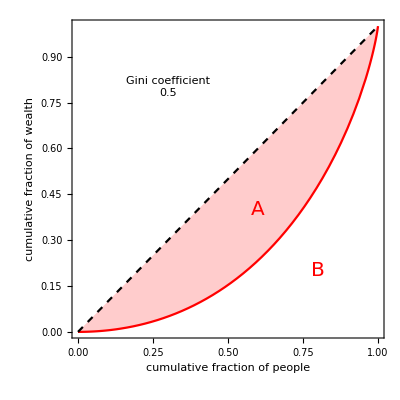

```mathematica
gini=1.-2*Integrate[Le[z],{z,0,1}];
pltheo=Show[Plot[{Le[z],z},{z,0,1},PlotStyle->{Red,{Black,Dashed}},Filling->{1->{2}}],Graphics[{Text["Gini coefficient\n"<>ToString[gini],{0.3,0.8}],Red,Text[Style["A",20],{0.6,0.4}],Text[Style["B",20],{0.8,0.2}]}],AspectRatio->1,PlotRange->{{0,1},{0,1}},FrameLabel->{"cumulative fraction of people","cumulative fraction of wealth"},PlotRangePadding->0]
```

The Gini coefficient is then given by

```mathematica
G = 1/μ∫_0^∞ F(x)(1- F(x)) dx =1-2∫_0^1 L(z) dz =((|A|)/(|A|+|B|)) .
```

To get the Lorenz curve from a given dataset (x_1,...,x_n) we sort the data into the order statistic (x_(1),...,x_(n)) and compute the partial sums s_k=∑_(i=1)^k x_(i). We get the Lorenz curve by plotting s_k/s_n against k/n.

```mathematica
ll=2;
data=RandomVariate[ExponentialDistribution[ll],100];
```

```mathematica
sorted=Accumulate[Sort[data]];
lorenz=Transpose[{Table[k,{k,0.01,1,0.01}],sorted/Max[sorted]}];
pldata=ListPlot[lorenz,PlotMarkers->"■",ImageSize->Medium]
```

-Graphics-

```mathematica
Show[pltheo,pldata]
```

-Graphics-

```mathematica
Sum[Abs[data[[k]]-data[[l]]],{k,1,Length[data]},{l,1,Length[data]}]/Mean[data]/Length[data]^2/2
```

0.527466

Let’s look at the Pareto distribution

```mathematica
PDF[ParetoDistribution[b,a],y]
```

Piecewise[{{a b^a y^(-1-a), y≥b}, {0, True}}]

```mathematica
CDF[ParetoDistribution[b,a],y]
```

Piecewise[{{1-(b/y)^a, y≥b}, {0, True}}]

```mathematica
Mean[ParetoDistribution[b,a]]
```

Piecewise[{{(a b)/(-1+a), a>1}, {Indeterminate, True}}]

```mathematica
f[y_]=Simplify[PDF[ParetoDistribution[b,a],y],b>0&&a>0&&y>b]
```

a b^a y^(-1-a)

```mathematica
s[x_]=Integrate[y*f[y],{y,b,x},Assumptions->{b>0&&x>b}]/Integrate[y*f[y],{y,b,Infinity},Assumptions->{b>0&&x>b&&a>1}]
```

(x^-a (-b^a x+b x^a))/b

```mathematica
inv[x_]=Solve[Simplify[CDF[ParetoDistribution[b,a],y],b>0&&a>0&&y>b]==x,y][[1,1,2]]
```

b (1-x)^(-1/a)

```mathematica
L[z_,b_,a_]=FullSimplify[s[inv[z]],b>0]
```

1-((1-z)^(-1/a))^(1-a)

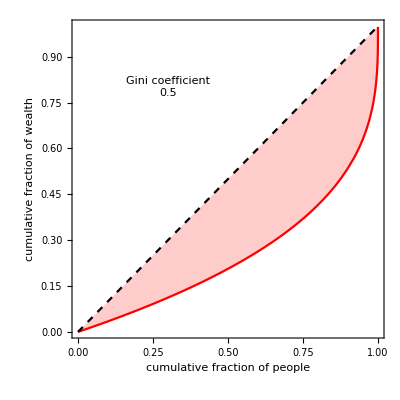

```mathematica
bb=1;aa=1.5;
gini=1.-2*Integrate[L[z,bb,aa],{z,0,1}];
pltheo=Show[Plot[{L[z,bb,aa],z},{z,0,1},PlotStyle->{Red,{Black,Dashed}},Filling->{1->{2}}],Graphics[{Text["Gini coefficient\n"<>ToString[gini],{0.3,0.8}]}],AspectRatio->1,Axes->False,Frame->True,PlotRange->{{0,1},{0,1}},FrameLabel->{"cumulative fraction of people","cumulative fraction of wealth"},BaseStyle->12,PlotRangePadding->0]
```

```mathematica
data=RandomVariate[ParetoDistribution[bb,aa],100];
sorted=Accumulate[Sort[data]];
lorenz=Transpose[{Table[k,{k,0.01,1,0.01}],sorted/Max[sorted]}];
pldata=ListPlot[lorenz,PlotMarkers->"■"]
```

-Graphics-

```mathematica
Show[pltheo,pldata]
```

-Graphics-

```mathematica
Sum[Abs[data[[k]]-data[[l]]],{k,1,Length[data]},{l,1,Length[data]}]/Mean[data]/Length[data]^2/2
```

0.546969

## Income and wealth data

```mathematica
data=ReadList["income_2005.txt",Number]
```

{5200,5510,5800,6070,6350,6630,6910,7170,7400,7610,7810,8020,8220,8430,8630,8850,9050,9270,9490,9700,9930,10100,10400,10600,10800,11000,11300,11500,11700,11900,12100,12400,12600,12900,13100,13300,13600,13800,14100,14400,14600,14900,15100,15400,15700,16000,16300,16600,16800,17100,17400,17700,18000,18400,18700,19000,19300,19700,20000,20400,20700,21100,21600,22000,22400,22800,23300,23700,24200,24700,25200,25700,26300,26800,27400,28100,28700,29400,30100,30800,31500,32400,33300,34200,35100,36200,37200,38400,39700,41300,43200,45500,48200,51800,56200,62500,72200,89800,132000}

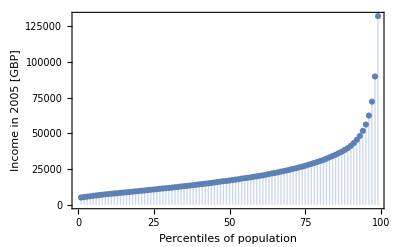

```mathematica
ListPlot[data,Filling->Axis,PlotRange->All,FrameLabel->{"Percentiles of population","Income in 2005 [GBP]"}]
```

```mathematica
Length[data]
```

99

```mathematica
sorted=Accumulate[Sort[data]];
lorenz=Transpose[{Table[k,{k,0.01,0.99,0.01}],sorted/Max[sorted]}];
Show[Plot[x,{x,0,1},PlotStyle->Black],ListPlot[lorenz,PlotMarkers->"■"],AspectRatio->1,FrameLabel->{"cumulative fraction of population","cumulative fraction of income"},PlotRangePadding->0]
```

-Graphics-

```mathematica
Sum[Abs[data[[k]]-data[[l]]],{k,1,Length[data]},{l,1,Length[data]}]/Mean[data]/Length[data]^2/2//N
```

0.340833

```mathematica
data=ReadList["income_2015.txt",Number];
```

```mathematica
tail15=Transpose[{data,Table[1-k/100,{k,1,99}]}];
```

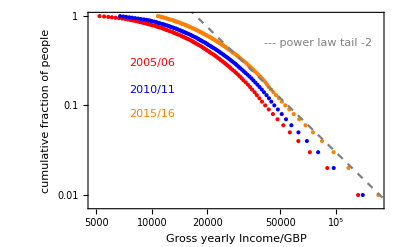

```mathematica
Show[ListLogLogPlot[{tail05,tail10,tail15},PlotStyle->{Red,Blue,Orange}],LogLogPlot[{300000000*x^(-2)},{x,5000,200000},PlotStyle->{Dashed,Gray}],Graphics[{Gray,Text["--- power law tail -2",{Log[80000],Log[0.5]}],Red,Text["2005/06",{Log[10000],Log[0.3]}],Blue,Text["2010/11",{Log[10000],Log[0.15]}],Orange,Text["2015/16",{Log[10000],Log[0.08]}]}],Axes->False,Frame->True,FrameLabel->{"Gross yearly Income/GBP","cumulative fraction of people"},BaseStyle->{12}]
```

```mathematica
dataw=ReadList["wealth_1416.txt",{Number,Number}];
```

```mathematica
Length[dataw]
```

18133

```mathematica
rich=Take[dataw,{Length[dataw]-20,Length[dataw]}]
```

{{97.146,99.949},{97.16,99.95},{97.223,99.953},{97.246,99.954},{97.306,99.956},{97.364,99.959},{97.5,99.965},{97.529,99.966},{97.636,99.97},{97.675,99.972},{97.881,99.979},{97.93,99.981},{97.961,99.982},{98.058,99.985},{98.203,99.988},{98.287,99.991},{98.376,99.992},{98.502,99.995},{98.781,99.997},{99.476,99.999},{100,100}}

```mathematica
dataw=Join[Take[dataw,{858,Length[dataw]-21,10}],rich];
```

```mathematica
Length[dataw]
```

1747

```mathematica
dataw=Transpose[{dataw[[All,2]],dataw[[All,1]]}]/100;
```

```mathematica
dataw[[1]]
```

{0.07883,0}

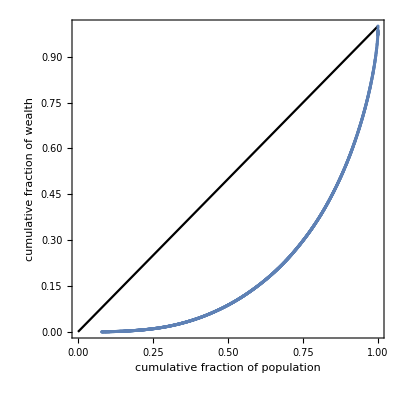

```mathematica
Show[Plot[x,{x,0,1},PlotStyle->Black],ListPlot[dataw],AspectRatio->1,FrameLabel->{"cumulative fraction of population","cumulative fraction of wealth"},PlotRangePadding->0]
```

```mathematica
diff=Differences[dataw];
```

```mathematica
Length[diff]
```

1746

```mathematica
1-2*Sum[(dataw[[k,2]]+dataw[[k+1,2]])/2*diff[[k,1]],{k,1,Length[diff]}]
```

0.620313

The slope of the Lorenz curve properly scaled gives (weighted) data points, which we can plot against the cumulative fraction of the population to obtain the tail distribution of the data.

```mathematica
shit1=0;shit2=0;taild={};For[k=1,k≤Length[diff],k++,If[diff[[k,1]]>0,taild=Join[taild,{{diff[[k,2]]*12778000000000/diff[[k,1]]/25916000,1-dataw[[k,1]]}}],shit1+=diff[[k,2]];shit2++]
];
{shit1,shit2}
```

{0,0}

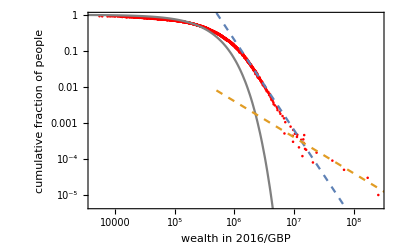

```mathematica
Show[ListLogLogPlot[taild,PlotStyle->Red],pltheo1,pltheo2,FrameLabel->{"wealth in 2016/GBP","cumulative fraction of people"}]
```

```mathematica
taild[[597]]
```

{246527.,1/2}

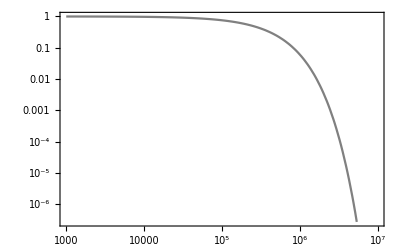

```mathematica
pltheo1=LogLogPlot[Exp[-x/246527*Log[2]],{x,1000,10000000},PlotStyle->Gray]
```

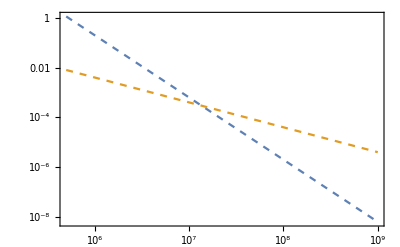

```mathematica
pltheo2=LogLogPlot[{x^(-2.5)*2*10^14,x^(-1)*4*10^3},{x,500000,1000000000},PlotStyle->Dashed]
```